```mathematica
SetDirectory[NotebookDirectory[]];
```

## Set wire data

```mathematica
r=0.127;
a=0.14019705362149942;
b=0.10709620563780475;
(*b=a;
a=0.10709620563780475;*)
n=64;
dt=(2π)/n;
tf=4 π/2;
```

Scan for extreme points

```mathematica
cdata=Table[{r Cos[t],r Sin[t]},{t,0,tf,dt}]//N;
bcdata={};

indexes={};
c=0;
For[i=1,i≤ Length[cdata],i++,
xwire=cdata[[i]];
InsideEllipseQ=(xwire[[1]]-0.0)^2/a^2+(xwire[[2]]-0.0)^2/b^2≤ 1.0;
If[a>b,
If[InsideEllipseQ,
If[c==1||c==3,AppendTo[indexes,i-1];c++;];
,
If[c==0||c==2,AppendTo[indexes,i];c++;];
];
,
If[InsideEllipseQ,
If[c==0||c==2,AppendTo[indexes,i-1];c++;];
,
If[c==1||c==3,AppendTo[indexes,i];c++;];
];
];
];
```

```mathematica
Print["Principal points = ",indexes];
```

Principal points = {7,27,39,59}

Case a>b

```mathematica
dt=(2π)/n;
ellipsepts={};

If[a>b,
ts=0.0;
c=1;
index=indexes[[c]];
xwirec=cdata[[index]];
For[k=1,k≤n,k++,
te=ts+dt*(k-1);
xe={ a Cos[te],b Sin[te] };
If[xe[[2]]<xwirec[[2]],
AppendTo[ellipsepts,xe];,
c++;
Break[];
];
];

ellipsepts;
q1=ellipsepts;
q2=Reverse[q1];
q2[[All,1]]=-1.0q2[[All,1]];
q3=Drop[q2,-1];
q3[[All,2]]=-1.0q3[[All,2]];
q4=Drop[Reverse[q1],-1];
q4[[All,2]]=-1.0q4[[All,2]];

,

c=1;
index=indexes[[c]];
xwirec=cdata[[index]];
ts=ArcCos[xwirec[[1]]/a];
c=2;
index=indexes[[c]];
xwirec=cdata[[index]];
For[k=1,k≤n,k++,
te=ts+dt*(k-1);
xe={ a Cos[te],b Sin[te] };
If[xe[[1]]>xwirec[[1]],
AppendTo[ellipsepts,xe];,
c++;
Break[];
];
];

ellipsepts;
q1=ellipsepts;
q2=Reverse[q1];
q2[[All,1]]=-1.0q2[[All,1]];
q2[[All,2]]=-1.0q2[[All,2]];
];
```

```mathematica
c=0;
bcdata={};
For[i=1,i≤ Length[cdata],i++,
xwire=cdata[[i]];
InsideEllipseQ=(xwire[[1]]-0.0)^2/a^2+(xwire[[2]]-0.0)^2/b^2≤ 1.0;
If[InsideEllipseQ,
If[a>b,
If[c==0,
For[k=1,k≤ Length[q1],k++,
AppendTo[bcdata,q1[[k]]];
];
c++;
Continue[];
];
If[c==1,
For[k=1,k≤ Length[q2],k++,
AppendTo[bcdata,q2[[k]]];
];
For[k=1,k≤ Length[q3],k++,
AppendTo[bcdata,q3[[k]]];
];
c++;
Continue[];
];
If[c==2,
For[k=1,k≤ Length[q4],k++,
AppendTo[bcdata,q4[[k]]];
];
c++;
Continue[];
];
,
If[c==0,
For[k=1,k≤ Length[q1],k++,
AppendTo[bcdata,q1[[k]]];
];
c++;
Continue[];
];
If[c==1,
For[k=1,k≤ Length[q2],k++,
AppendTo[bcdata,q2[[k]]];
];
c++;
Continue[];
];
];
,
AppendTo[bcdata,xwire];
];
];
```

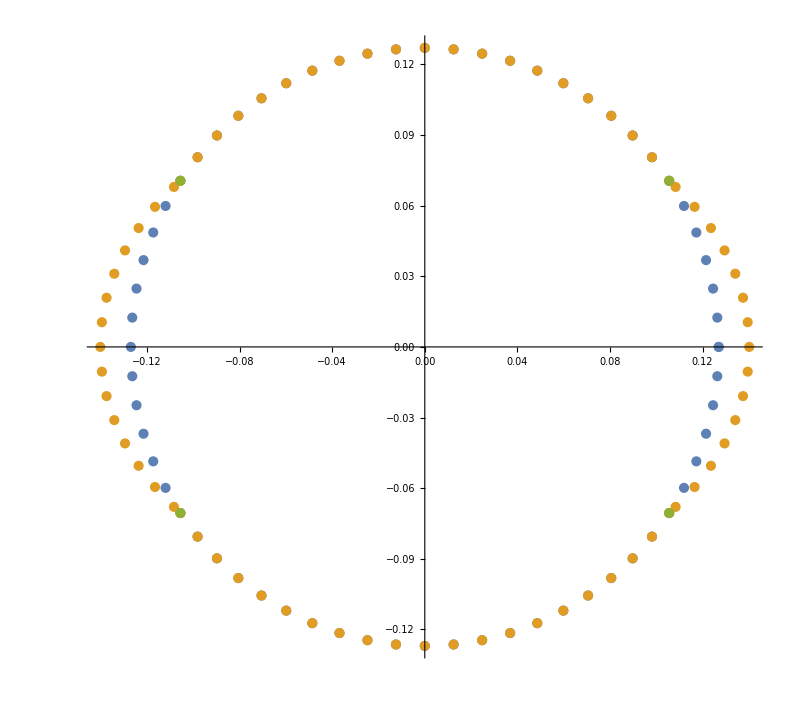

```mathematica
ListPlot[{cdata,bcdata,cdata[[indexes]]},AspectRatio->Automatic,Joined->{False,False}]
```

Appending third coordinate

```mathematica
data=Table[{data[[i,1]],data[[i,2]],0.0},{i,1,Length[data]-1}];
```

## Exporting wire

```mathematica
(*Export["internal_wire.dat",data];*)
```